### Model

```mathematica
(*Returns True if the input state is valid and false otherwise*)
checkState[state_]:= Module[
{numberlist = Flatten[state]},
(*We must check that:
1. There are 4 sublists
2. Each of these sublists has 4 elements.
3. Each number is used exactly once
4. Only numbers from 1 to 15, and -1 are used
*)
If[Length[state]≠ 4, Return[False]
];
If[Length[state[[1]]] ≠ 4 || Length[state[[2]]] ≠ 4 || Length[state[[3]]] ≠ 4|| Length[state[[4]]]≠ 4, Return[False]
];
If[Length[DeleteDuplicates[Flatten[state]]]≠ 16, Return[False]
];
If[Length[Select[numberlist,MemberQ[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,-1},#]== False&]] ≠ 0,Return[False]];
Return[True]
]
```

```mathematica
checkState[{{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}}]
```

True

```mathematica
checkState[{{1,2,3,4},{9,10,12,11},{-1,5,6,7},{13,14,15,8}}]
```

True

```mathematica
checkState[{{1,2,3,4},{-1,10,12,11},{-1,5,6,7},{13,14,15,8}}]
```

False

```mathematica
goal ={{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,-1}};
```

```mathematica
(*Checks whether a given state is the goal.*)
isGoalState[state_]:= If[state ==goal, Return[True], Return[False] ]
```

```mathematica
isGoalState[goal]
```

True

```mathematica
isGoalState[{{1,2,3,4},{9,10,12,11},{-1,5,6,7},{13,14,15,8}}]
```

False

```mathematica
(*Checks whether the input move is valid for the input state*)
isValidMove[state_, move_]:= Module[{blankCoordinates = emptySquareLocation[state]},
If[checkState[state]== False, Return[False]];
(*Checks whether the move is one of the allowed moves--must move at most 1 in either direction*)
If[MemberQ[{{-1,0},{1,0},{0,1},{0,-1}},move] == False, Return[False]];
(*Checks whether the move will leave the blank space within the bounds of the puzzle*)
If[MemberQ[{1,2,3,4},blankCoordinates[[1]]+move[[1]]] == True && MemberQ[{1,2,3,4},blankCoordinates[[2]]+move[[2]]]  == True,
Return[True],
Return[False]
]
]
```

```mathematica
state1={{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}};
isValidMove[state1, {0, -1}]
```

True

```mathematica
state2={{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}};
isValidMove[state2, {0, 1}]
```

False

```mathematica
(*Locates the row and column of the -1 in the puzzle and returns its row and column as an ordered pair.*)
emptySquareLocation[state_]:=Module[{row = 1,col = 1, coordinatesOfBlank = {}, correctRow = {}},
If[checkState[state]==False, Return[0]];
(*Search for the row of the -1*)
While[row≤ 4,
If[MemberQ[state[[row]],-1],
correctRow = state[[row]]; Break[]];
row++;
];
(*Search for the column of the -1*)
While[col ≤ 4,
If[correctRow[[col]] == -1, 
(*If the column has been located, return the ordered pair.*)
coordinatesOfBlank = {row,col};
Return[coordinatesOfBlank]];
   col++
];
]
```

```mathematica
emptySquareLocation[{{1,2,3,4},{9,10,12,11},{-1,5,6,7},{13,14,15,8}}]
```

{3,1}

```mathematica
emptySquareLocation[{{1,2,3,4},{9,10,12,11},{13,14,15,8},{5,-1,6,7}}]
```

{4,2}

```mathematica
(*Outputs the updated state of the puzzle, and a boolean representing whether the puzzle is solved, after the specified move has been made*)
makeMove[state_, move_]:= Module[
{isSolved, updatedState = state, 
blank = emptySquareLocation[state]},
If[isValidMove[state, move]== False, 
If[isGoalState[state]== True,
isSolved = True,
isSolved = False
],
(*Where the blank used to be, replace with the appropriate number*)
updatedState[[blank[[1]],blank[[2]]]] = state[[blank[[1]]+move[[1]], blank[[2]]+move[[2]]]];
updatedState[[blank[[1]]+move[[1]],blank[[2]]+move[[2]]]] = -1;
If[isGoalState[updatedState] == True,
(*Set isSolved to the appropriate value*)
isSolved = True,
isSolved = False
]
];
Return[{isSolved, updatedState}]
]
```

```mathematica
emptySquareLocation[state3]
```

{3,4}

```mathematica
state3={{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}};
makeMove[state3, {0, -1}]
```

{False,{{1,2,3,4},{5,6,7,8},{9,10,-1,11},{13,14,15,12}}}

```mathematica
makeMove[state3,{-1,0}]
```

{False,{{1,2,3,4},{5,6,7,-1},{9,10,11,8},{13,14,15,12}}}

```mathematica
makeMove[state3,{-1,-1}]
```

{False,{{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}}}

### Controller

```mathematica
(*Returns the center of a square specified by the input row and column.*)
findTileCenter[{row_,col_}]:= {col-0.5, 4.5-row}
```

```mathematica
findTileCenter[{1,2}]
```

{1.5,3.5}

```mathematica
findTileCenter[{4,4}]
```

{3.5,0.5}

```mathematica
(*Finds the row and column of a point*)
findTile[{xVal_,yVal_}]:= {4-Floor[yVal],Ceiling[xVal]}
```

```mathematica
findTile[{3.5,0.5}]
```

{4,4}

```mathematica
findTile[{2.6,3.7}]
```

{1,3}

```mathematica
(*Outputs the change needed in row and column for the empty tile to be moved to the specified position*)
translateMove[{xDistance_, yDistance_}]:= {-yDistance, xDistance}
```

```mathematica
translateMove[{0,1}]
```

{-1,0}

```mathematica
translateMove[{1,0}]
```

{0,1}

```mathematica
translateMove[{2,3}]
```

{-3,2}

```mathematica
(*Creates a list of 16 elements, one for each tile; each element contains the number in that tile, paired with the center coordinates of the tile*)
translateToView[state_]:= Module[
{outputList = {}, indexRow = 1,indexCol = 1},
While[indexRow ≤ 4,
(*Start at the first element of the row*)
indexCol = 1;
While[indexCol ≤ 4,
(*Append each of the elements for the row to the list*)
AppendTo[outputList, {state[[indexRow, indexCol]],findTileCenter[{indexRow, indexCol}]}];
indexCol++
];
indexRow++
];
Return[outputList]
]
```

```mathematica
goal
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,-1}}

```mathematica
tileLst=translateToView[goal]
```

{{1,{0.5,3.5}},{2,{1.5,3.5}},{3,{2.5,3.5}},{4,{3.5,3.5}},{5,{0.5,2.5}},{6,{1.5,2.5}},{7,{2.5,2.5}},{8,{3.5,2.5}},{9,{0.5,1.5}},{10,{1.5,1.5}},{11,{2.5,1.5}},{12,{3.5,1.5}},{13,{0.5,0.5}},{14,{1.5,0.5}},{15,{2.5,0.5}},{-1,{3.5,0.5}}}

```mathematica
translateToView[state1]
```

{{1,{0.5,3.5}},{2,{1.5,3.5}},{3,{2.5,3.5}},{4,{3.5,3.5}},{5,{0.5,2.5}},{6,{1.5,2.5}},{7,{2.5,2.5}},{8,{3.5,2.5}},{9,{0.5,1.5}},{10,{1.5,1.5}},{11,{2.5,1.5}},{-1,{3.5,1.5}},{13,{0.5,0.5}},{14,{1.5,0.5}},{15,{2.5,0.5}},{12,{3.5,0.5}}}

```mathematica
processMoveRequest[{xDist_, yDist_}]:=
```

### View

```mathematica
(* turns tileLst into Graphics primitives *)
createGraphisLstView1[tileLst_]:=
Table[Text[Style[tileLst[[cnt,1]],Large], tileLst[[cnt, 2]]], {cnt,Length@tileLst}]
```

```mathematica
u=createGraphisLstView1[tileLst]
```

{Text[1,{0.5,3.5}],Text[2,{1.5,3.5}],Text[3,{2.5,3.5}],Text[4,{3.5,3.5}],Text[5,{0.5,2.5}],Text[6,{1.5,2.5}],Text[7,{2.5,2.5}],Text[8,{3.5,2.5}],Text[9,{0.5,1.5}],Text[10,{1.5,1.5}],Text[11,{2.5,1.5}],Text[12,{3.5,1.5}],Text[13,{0.5,0.5}],Text[14,{1.5,0.5}],Text[15,{2.5,0.5}],Text[-1,{3.5,0.5}]}

```mathematica
FullForm[u[[2]]]
```

Text[Style[List[2,List[1.5,3.5]],Large]]

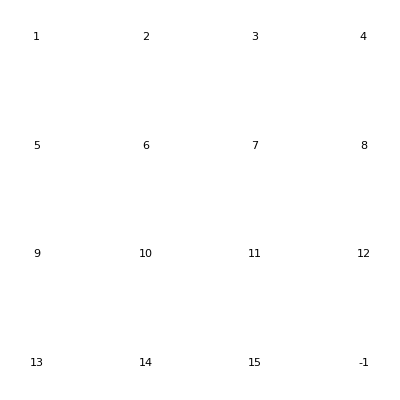

```mathematica
Graphics[u]
```

```mathematica
displayPuzzleView1[tileLst_, done_]:=Graphics[{
{Yellow, Rectangle[{0,0}, {4,4}]},createGraphisLstView1[tileLst],
If[done==True, {Blue,Text[Style["You are a winner!!!", Large],{2,2}]}
]
}
]
```

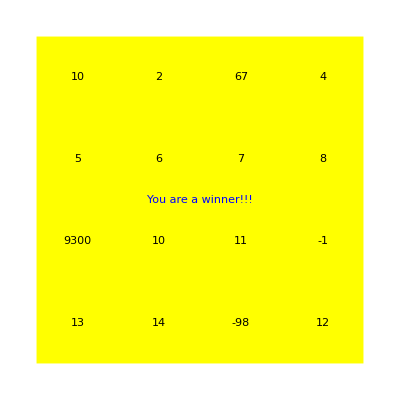

```mathematica
displayPuzzleView1[tileLst,True]
```

```mathematica
listToState[tileLst_]:=Partition[Table[tileLst[[cnt, 1]], {cnt, Length@tileLst}],4]
```

```mathematica
listToState[tileLst]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,-1}}

```mathematica
tileLst=translateToView[{{10,2,67,4},{5,6,7,8},{9300,10,11,-1},{13,14,-98,12}}];
```

```mathematica
Dynamic[tileLst]
```

```mathematica
{{1,{0.5,3.5}},{2,{1.5,3.5}},{67,{2.5,3.5}},{,{3.5,3.5}},{5,{0.5,2.5}},{6,{1.5,2.5}},{7,{2.5,2.5}},{8,{3.5,2.5}},{9,{0.5,1.5}},{10,{1.5,1.5}},{11,{2.5,1.5}},{-1,{3.5,1.5}},{13,{0.5,0.5}},{14,{1.5,0.5}},{15,{2.5,0.5}},{12,{3.5,0.5}}}
```

```mathematica
display2test[tileLst_]:= DynamicModule[{tempList=tileLst, state=listToState[tileLst]}, 
displayPuzzleView1[tempList,False]]
```

```mathematica
Dynamic[display2test[tileLst]]
```

```mathematica
display2test[tileLst]
```

```mathematica
tileLst = {{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}}
```

{{1,2,3,4},{5,6,7,8},{9,10,11,-1},{13,14,15,12}}

```mathematica
playPuzzleView1[tileLst_]:=DynamicModule[
{tempList=tileLst, state, move},
displayPuzzleView1[tileLst,True];
state=listToState[tempList];
Print[state];
Print[isGoalState[state]];
displayPuzzleView1[tileLst,True];
(*makeMove[state,move];*)
tempList=translateToView[state];
Column[{Button["up", state = makeMove[state, {-1,0}]], Button["down",state = makeMove[state, {1,0}]],Button["left",state = makeMove[state, {0,-1}]],Button["right",state = makeMove[state, {0,1}]]}]
(*displayPuzzleView1[*)
]
```

```mathematica
Dynamic[displayPuzzleView1[tileLst]]
```

```mathematica
o=playPuzzleView1[tileLst]
```

{{10,2,67,4},{5,6,7,8},{9300,10,11,-1},{13,14,-98,12}}

False

```mathematica
FullForm[o]
```

DynamicModule[List[Set[tempList,List[List[1,List[0.5,3.5]],List[2,List[1.5,3.5]],List[3,List[2.5,3.5]],List[4,List[3.5,3.5]],List[5,List[0.5,2.5]],List[6,List[1.5,2.5]],List[7,List[2.5,2.5]],List[8,List[3.5,2.5]],List[9,List[0.5,1.5]],List[10,List[1.5,1.5]],List[11,List[2.5,1.5]],List[12,List[3.5,1.5]],List[13,List[0.5,0.5]],List[14,List[1.5,0.5]],List[15,List[2.5,0.5]],List[-1,List[3.5,0.5]]]],Set[state,List[List[1,2,3,4],List[5,6,7,8],List[9,10,11,12],List[13,14,15,-1]]],move],Column[List[Button["up",makeMove[state,List[-1,0]]],Button["down",makeMove[state,List[1,0]]],Button["left",makeMove[state,List[0,-1]]],Button["right",makeMove[state,List[0,1]]]]],RuleDelayed[DynamicModuleValues,List[]]]

```mathematica
?Button
```

Button[label,action] represents a button that is labeled with label, and evaluates action whenever it is clicked.

```mathematica
makeGraphicsLst[diskLst_]:=
Table[{diskLst[[pos,1]],Disk[diskLst[[pos,2]],0.3]}, {pos,Length@diskLst}]
```

```mathematica
tileLst
```

{{10,{0.5,3.5}},{2,{1.5,3.5}},{67,{2.5,3.5}},{4,{3.5,3.5}},{5,{0.5,2.5}},{6,{1.5,2.5}},{7,{2.5,2.5}},{8,{3.5,2.5}},{9300,{0.5,1.5}},{10,{1.5,1.5}},{11,{2.5,1.5}},{-1,{3.5,1.5}},{13,{0.5,0.5}},{14,{1.5,0.5}},{-98,{2.5,0.5}},{12,{3.5,0.5}}}

```mathematica
createGraphisLstView2[tileLst_]:=
Table[{tileLst[[cnt, 1]], 
Disk[tileLst[[cnt, 2]], 
If[tileLst[[cnt,1]]≠-1,tileLst[[cnt,1]]*.05,0]
]
}, {cnt, Length@tileLst}]
```

```mathematica
createGraphisLstView2[translateToView[goal]]
```

{{1,Disk[{0.5,3.5},0.05]},{2,Disk[{1.5,3.5},0.1]},{3,Disk[{2.5,3.5},0.15]},{4,Disk[{3.5,3.5},0.2]},{5,Disk[{0.5,2.5},0.25]},{6,Disk[{1.5,2.5},0.3]},{7,Disk[{2.5,2.5},0.35]},{8,Disk[{3.5,2.5},0.4]},{9,Disk[{0.5,1.5},0.45]},{10,Disk[{1.5,1.5},0.5]},{11,Disk[{2.5,1.5},0.55]},{12,Disk[{3.5,1.5},0.6]},{13,Disk[{0.5,0.5},0.65]},{14,Disk[{1.5,0.5},0.7]},{15,Disk[{2.5,0.5},0.75]},{-1,Disk[{3.5,0.5},0]}}

```mathematica
findSquareCenter[{xVal_,yVal_}]:={4-Floor[yVal],Ceiling[xVal]}
```

```mathematica
displayPuzzleView2[tileLst_, done_]:=
```